# RABBIT: Reconstructing Ancestry Blocks BIT by bit in multiparental populations

## Chaozhi Zheng Biometris, Wageningen UR May 4, 2014

## Helps on “MagicReconstruct`”

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]<>"\\RABBIT_Packages"];
Needs["MagicReconstruct`"]
SetDirectory[NotebookDirectory[]];
?"MagicReconstruct`*"
```

```mathematica
?magicReconstruct
```

magicReconstruct[magicSNP, model, epsF, eps, popDesign, outputfile] reconstructs the ancestral origins in multi-parental populations. magicSNP is the input marker data, which are analyzed under the model using a HMM algorithm HMMMethod. The parameters epsF and eps refer to the allelic typing errors for founders and sampled individuals, respectively. The parameter popDesign can be either a list of mating schemes of the mapping population until the last generation, or the list of values denoting the junction distribution. The results are saved in outputfile. 
 magicReconstruct[magicSNPfile, model, epsF, eps, popDesign, outfile] where the input marker data are privided as the filename magicSNPfile.

```mathematica
Options[magicReconstruct]
```

{HMMMethod→origPathSampling,SampleSize→1000,PrintTimeElapsed→False}

```mathematica
?HMMMethod
```

HMMMethod is an option to specify the alogrithm used for Hidden Markov Model, it has to be one of "origPathSampling", "origPosteriorDecoding", or "origViterbiDecoding".

## Example data: simulated CC

Consider two males and two females  are sampled independently from CC funnels at generation F11. The true allelic error probabilitis are 0.005 for both founders and samples. One pair of autosomes and One pair of sex chromosomes.

```mathematica
magicSNP=Import["MagicReconstruct_Input_ExampleCC.csv"];
magicSNP[[1]]
magicSNP[[2;;, ;;;;Round[Last[Dimensions[Rest[magicSNP]]]/9]]]//TableForm
```

{#founders,8}

SNP | UNC011275068 | UNC011510234 | UNC010259898 | backuprs32565732 | JAX00709389 | UNC200093280 | UNC200108569 | UNC200036229 | JAX00187177
Chromosome | 1 | 1 | 1 | 1 | X | X | X | X | X
cM | 22.8 | 41.8223 | 64.1278 | 83.8805 | 6.12812 | 28.6456 | 46.7543 | 63.5105 | 82.6962
A/J | 1 | 2 | 1 | 2 | 1 | N | 1 | 1 | 2
C57BL/6J | 1 | 2 | 2 | 2 | 1 | N | 1 | 1 | 2
129S1/SvImJ | 1 | 2 | 1 | 2 | N | N | 1 | 2 | 1
NOD/ShiLtJ | 1 | 2 | 1 | 1 | 1 | N | 1 | 1 | 1
NZO/HlLtJ | 2 | 2 | N | 2 | N | 1 | 1 | 1 | 1
CAST/EiJ | 2 | 1 | 1 | 1 | N | 1 | 1 | 2 | 1
PWK/PhJ | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1
WSB/EiJ | 2 | 1 | 2 | 2 | N | 1 | 1 | 1 | 1
Line1 | 11 | 22 | 11 | 11 | 1 | N | 1 | 1 | 2
Line2 | 22 | 11 | 11 | 11 | NN | NN | 11 | 11 | 11
Line3 | 22 | 22 | 11 | 21 | 1 | 1 | 1 | 2 | 1
Line4 | 21 | 22 | NN | 22 | 11 | 11 | 11 | 11 | 11

Input CSV formatted data

Row 1 species the number of founder strains

The rest shows as a matrix for genetic map and SNP data for founders and sampled individuals. The X chromsomes have to named as “X” or “x”.

Let 1 and 2 denote the two alleles of SNPs, and N for missing alleles. The founders and male X chromosomes are shown as haplotypes.

## Posterior decoding

Set the input parameters: popDesign, epsF, eps, model, inputfile, and outputfile.

```mathematica
popScheme=Join[Table["Pairing",{2}],Table["Sibling",{9}]]
epsF=eps=0.005;
model="jointModel";
estfun="origPosteriorDecoding";
outputfile="MagicReconstruct_Output_ExampleCC_"<>model<>"_"<>estfun<>".txt"
inputfile="MagicReconstruct_Input_ExampleCC.csv"
```

{Pairing,Pairing,Sibling,Sibling,Sibling,Sibling,Sibling,Sibling,Sibling,Sibling,Sibling}

MagicReconstruct_Output_ExampleCC_jointModel_origPosteriorDecoding.txt

MagicReconstruct_Input_ExampleCC.csv

```mathematica
magicReconstruct[inputfile,model,epsF,eps,popScheme,outputfile,HMMMethod->estfun,PrintTimeElapsed->True];
```

Start date =Mon 4 May 2015 09:23:23

Pre-computing data probability...	outputfile = MagicReconstruct_Output_ExampleCC_jointModel_origPosteriorDecoding.txt

Prior {f,j1122,j1211,j1213,j1222,j1232} =  {0.826172,3.70508,0.933594,0.517578,0.933594,0.517578}

Prior {fmp,j1122mp,j1211mp,j1213mp,j1222mp,j1232mp} = {0.826172,2.41992,0.630859,0.291016,0.695313,0.292969}

Done! Finished date =Mon 4 May 2015 09:23:25. 	Time elapsed = 1.9 Seconds.

## Conidtional posterior probability

Summary the output of magicReconstruct.

```mathematica
resultFile="MagicReconstruct_Output_ExampleCC_jointModel_origPosteriorDecoding.txt"; summaryFile=StringDrop[resultFile,-4]<>"_Summary.csv"; saveAsSummaryMR[resultFile,summaryFile];res=getSummaryMR[summaryFile];First[res]//TableForm
```

MagicReconstruct-Summary |  Genetic map of biallelic markers
MagicReconstruct-Summary |  Ln marginal likelihood
MagicReconstruct-Summary |  Genotypes in order
MagicReconstruct-Summary |  Conditonal genotype probability
MagicReconstruct-Summary |  haplotypes in order
MagicReconstruct-Summary |  Conditonal haplotype probability

Posterior genotype porbabilities at markers of each sampled lines.

```mathematica
types=origGenotypes[8];
truegeno=ToExpression[Import["MagicReconstruct_TrueDiplotype_ExampleCC.csv"][[4;;,2;;]]];
truegeno=(truegeno/.Thread[types[[1,2]]->Range[Length[types[[1,2]]]]])/.Thread[Range[Length[types[[2,2]]]]->types[[2,2]]];
gggenoprob=Table[
pos=Span@@{4+36 (line-1),3+36 line};
condprob=res[[5,pos,2;;]];
Show[
MatrixPlot[Reverse[condprob],FrameLabel->{"Genotypes","SNP"},ColorFunctionScaling->False,MaxPlotPoints->Infinity,AspectRatio->1/2.5,DataRange->{{1,Dimensions[condprob][[2]]},{1,Length[condprob]}}],
ListPlot[Transpose[{Range[Length[truegeno[[line]]]],truegeno[[line]]}],PlotRange->{{1,Dimensions[condprob][[2]]},{1,Length[condprob]}},PlotRangePadding->0,PlotMarkers->{"×",10},PlotStyle->Red],
ListLinePlot[Thread[{Count[res[[5,2,2;;]],res[[5,2,2]]],{1,Length[condprob]}}],PlotStyle->{Dashed,Thick}],
FrameTicks->{{Transpose[{Range[Length[types[[1,1]]]],types[[1,1]]}],None},{Automatic,None}},
ImageSize->900,Frame->True,PlotLabel->"Line "<>ToString[line]<>". GrayLevel=Posterior Probability, red X=True Genotype."
],{line,Length[truegeno]}];
ListAnimate[gggenoprob]
```

## Viterbi decoding

Estimate the optimal sequences by viterbi decoding and summary the output.

```mathematica
model="jointModel"; 
estfun="origViterbiDecoding";outputfile="MagicReconstruct_Output_ExampleCC_"<>model<>"_"<>estfun<>".txt";
magicReconstruct[inputfile,model,epsF,eps,popScheme,outputfile,HMMMethod->estfun,PrintTimeElapsed->True];
```

Start date =Mon 4 May 2015 09:23:30

Pre-computing data probability...	outputfile = MagicReconstruct_Output_ExampleCC_jointModel_origViterbiDecoding.txt

Prior {f,j1122,j1211,j1213,j1222,j1232} =  {0.826172,3.70508,0.933594,0.517578,0.933594,0.517578}

Prior {fmp,j1122mp,j1211mp,j1213mp,j1222mp,j1232mp} = {0.826172,2.41992,0.630859,0.291016,0.695313,0.292969}

Done! Finished date =Mon 4 May 2015 09:23:37. 	Time elapsed = 6.6 Seconds.

```mathematica
resultFile=outputfile; summaryFile=StringDrop[resultFile,-4]<>"_Summary.csv"; 
saveAsSummaryMR[resultFile,summaryFile]
res=getSummaryMR[summaryFile];First[res]//TableForm
```

MagicReconstruct-Summary |  Genetic map of biallelic markers
MagicReconstruct-Summary |  Ln marginal likelihood
MagicReconstruct-Summary |  haplotypes in order
MagicReconstruct-Summary |  diplotypes in order
MagicReconstruct-Summary |  Viterbi path of diplotypes

## Viterbi path

Viterbi path (tranformed from diplotypes into genotypes) at markers for each sampled lines.

```mathematica
ggviterbi=Table[
path=Flatten[Map[CtDiscreteFormat[CtJumpFormat[#]]&,StringSplit[res[[6,line+1,2]],"||"]]]/.Thread[Range[Length[types[[2,2]]]]->types[[2,2]]];
ListLinePlot[Transpose[{Range[Length[path]],path}],PlotRange->{{1,Dimensions[condprob][[2]]},{1,Length[condprob]}},PlotRangePadding->0,PlotStyle->Blue,PlotStyle->{Thick}],{line,Length[res[[6]]]-1}];
gg=Table[Show[gggenoprob[[line]],ggviterbi[[line]],PlotLabel->"Line "<>ToString[line]<>". GrayLevel=Posterior Probability, red X=True Genotype, blue line = Viterbi path"],{line,Length[ggviterbi]}];
ListAnimate[gg]
```

## Posterior sampling

Posterior sampling and summary the output.

```mathematica
model="jointModel";  estfun="origPathSampling";
outputfile="MagicReconstruct_Output_ExampleCC_"<>model<>"_"<>estfun<>".txt";
magicReconstruct[inputfile,model,epsF,eps,popScheme, outputfile,HMMMethod->estfun,SampleSize->20,PrintTimeElapsed->True];
```

Start date =Mon 4 May 2015 09:23:40

Pre-computing data probability...	outputfile = MagicReconstruct_Output_ExampleCC_jointModel_origPathSampling.txt

Prior {f,j1122,j1211,j1213,j1222,j1232} =  {0.826172,3.70508,0.933594,0.517578,0.933594,0.517578}

Prior {fmp,j1122mp,j1211mp,j1213mp,j1222mp,j1232mp} = {0.826172,2.41992,0.630859,0.291016,0.695313,0.292969}

Done! Finished date =Mon 4 May 2015 09:23:44. 	Time elapsed = 4.6 Seconds.

```mathematica
resultFile=outputfile; summaryFile=StringDrop[resultFile,-4]<>"_Summary.csv"; 
saveAsSummaryMR[resultFile,summaryFile]
res=getSummaryMR[summaryFile];First[res]//TableForm
```

MagicReconstruct-Summary |  Genetic map of biallelic markers
MagicReconstruct-Summary |  Ln marginal likelihood
MagicReconstruct-Summary |  haplotypes in order
MagicReconstruct-Summary |  diplotypes in order
MagicReconstruct-Summary |  Sampled paths of diplotypes

## Sampled path

20 randomly sampled path (tranformed from diplotypes into genotypes) at markers for line 1.

```mathematica
line=1;
paths=Flatten[#]&/@Map[CtDiscreteFormat[CtJumpFormat[#]]&,StringSplit[#,"|"]&/@StringSplit[res[[6,line+1,2]],"||"],{2}];
paths=paths/.Thread[Range[Length[types[[2,2]]]]->types[[2,2]]];
ggpaths=Table[
g=ListLinePlot[Transpose[{Range[Length[path]],path}],PlotRange->{{1,Dimensions[condprob][[2]]},{1,Length[condprob]}},PlotRangePadding->0,PlotStyle->Blue,PlotStyle->{Thick}];
g=Show[gggenoprob[[line]],g,PlotLabel->"Line "<>ToString[line]<>". GrayLevel=Posterior Probability, red X=True Genotype, blue line = Random sampled path"],{path,paths}];
ListAnimate[ggpaths]
```

## Multi-stage random mating populations

For multi-stage random mating populations with discrete generations, the input pop = popScheme can be specified by a list with ith (i = 1, ...) elemnt being the mating scheme producing the F_i (t=i) population. The founder population F_0 (t=0) consists of L inbred founders.

Example popScheme for common mapping populations.

Population type | #inbred founders L  | Example popScheme
CC (8-way RIL) | 8 | {Pairing,Pairing, Sibling,Sibling}
MAGIC | 19 | {FullDiallel,RM1-E,RM1-E, Selfing,Selfing}
AIL | 2 | {RM1-NE-100,RM1-E,RM1-E,Selfing,Selfing}
DSPR (one population) | 8 | {RM1-NE-500, RM1-E,RM1-E, Sibling,Sibling}
APRIL (4-way RIL) | 4 | {Pairing,Pairing, Selfing,Selfing}
Usered defined | 8 | {Pairing,RM1-E,Pairing,Sibling,Pairing, Selfing,Selfing}

“Selfing” and “Sibling” (mating) are the mating schemes for inbreeding stage to obtain homozygous lines. “Pairing” refers to exclusively pairingwise mating and each pair produce one offspring so that the population size descreases by half.

Random mating schemes can be choose from  “RM1-E”, “RM1-NE”, “RM2-E”, and “RM2-NE” where the population size is maitained constant. To change the populaiton size, “RM1-NE-N” or “RM2-NE-N” may be used so that the produced populaiton has size N.

## Diversity outcross populations

For the diversity outcross (DO), the founder pre-CC lines were in different inbreeding generations. Calcuate  analytically pop = Omega the process hyperparameter,

```mathematica
nPower=3;
preCCfreq={{4,0.14788732394366197},{5,0.4507042253521127},{6,0.16901408450704225},{7,0.07042253521126761},{8,0.035211267605633804},{9,0.06338028169014084},{10,0.02112676056338028},{11,0.02112676056338028},{12,0.02112676056338028}};
crossPopSize=334;
gCross=4;
crossScheme="RM1-E";
omega={magicOrigPriorDO[nPower,preCCfreq,crossPopSize,gCross,crossScheme],magicOrigPriorDOXY[nPower,preCCfreq,crossPopSize,gCross,crossScheme]}
```

{{0.127625,0.0203968,1.12526,6.71226,1.12526,6.71226},{0.128498,0.0150269,0.702863,4.19463,0.774589,4.60996}}

The hetergenous stocks (HS) is a speical case of DO

```mathematica
preCCfreqHS={{gpreCCinbred=1,1}};
omegaHS={magicOrigPriorDO[nPower,preCCfreqHS,crossPopSize,gCross,crossScheme],magicOrigPriorDOXY[nPower,preCCfreqHS,crossPopSize,gCross,crossScheme]}
```

{{0.127625,0.0129364,0.815301,4.85252,0.815301,4.85252},{0.128498,0.00839797,0.493683,2.93955,0.569533,3.37963}}

## Fixed breeding pedigree

Calculate pop = Omega by simulations of gene dropping on the pedigree.  Use the CC for an illustration.

popped: {generation, individual-ID, gender (1=female,2=male, 0=hermaphrodite), {mother-ID, father-ID}, Founder genome label)}

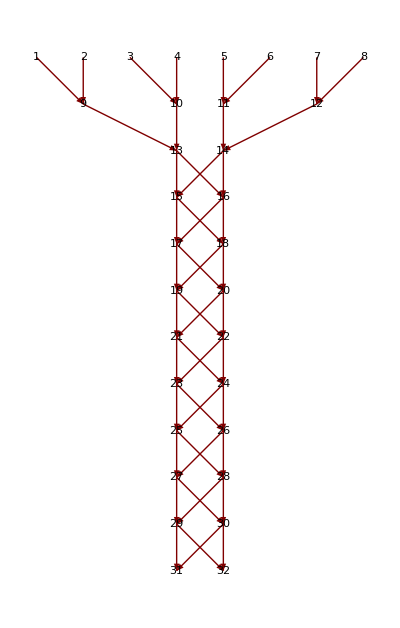
{(0 | 1 | 1 | {0,0} | {1,1}
0 | 2 | 2 | {0,0} | {2,2}
0 | 3 | 1 | {0,0} | {3,3}
0 | 4 | 2 | {0,0} | {4,4}
0 | 5 | 1 | {0,0} | {5,5}
0 | 6 | 2 | {0,0} | {6,6}
0 | 7 | 1 | {0,0} | {7,7}
0 | 8 | 2 | {0,0} | {8,8}
1 | 9 | 1 | {1,2} | NA
1 | 10 | 2 | {3,4} | NA
1 | 11 | 1 | {5,6} | NA
1 | 12 | 2 | {7,8} | NA
2 | 13 | 1 | {9,10} | NA
2 | 14 | 2 | {11,12} | NA
3 | 15 | 1 | {13,14} | NA
3 | 16 | 2 | {13,14} | NA
4 | 17 | 1 | {15,16} | NA
4 | 18 | 2 | {15,16} | NA
5 | 19 | 1 | {17,18} | NA
5 | 20 | 2 | {17,18} | NA
6 | 21 | 1 | {19,20} | NA
6 | 22 | 2 | {19,20} | NA
7 | 23 | 1 | {21,22} | NA
7 | 24 | 2 | {21,22} | NA
8 | 25 | 1 | {23,24} | NA
8 | 26 | 2 | {23,24} | NA
9 | 27 | 1 | {25,26} | NA
9 | 28 | 2 | {25,26} | NA
10 | 29 | 1 | {27,28} | NA
10 | 30 | 2 | {27,28} | NA
11 | 31 | 1 | {29,30} | NA
11 | 32 | 2 | {29,30} | NA),-Graphics-}

```mathematica
nFounder=8; founderFGL=Table[{i,i},{i,nFounder}];isOogamy=True; 
popPed=simPedigree[founderFGL,popScheme,isOogamy];
{popPed//MatrixForm,pedigreePlot[popPed,ImageSize->400]}
```

## Fixed breeding pedigree (cont.)

Calculate Omage by simulations for the CC

```mathematica
isOogamy=True; 
interferStrength=0; isObligate=False; 
chrLength={100,100}; (*cM*)
(*increase the sample size for real application, for example 10000*)
sampleSize=200;
omega=pedOrigPrior[popPed,chrLength,interferStrength,isObligate,isOogamy,sampleSize];//AbsoluteTiming
omega
```

{11.99,Null}

{{0.81,3.765,0.8625,0.5675,1.00375,0.5125},{0.83,2.42,0.6375,0.24,0.7675,0.325}}

The internal functions for the CC

```mathematica
omega2={magicOrigPrior[nFounder,popScheme],magicOrigPriorXY[nFounder,popScheme]}
```

{{0.826172,3.70508,0.933594,0.517578,0.933594,0.517578},{0.826172,2.41992,0.630859,0.291016,0.695313,0.292969}}

Note that the simulated omega will be different from the analytic omega if the breeding pedigree is not completely determined by the popScheme.

## Estimate the autosomal map expansion

Calculate autosmal map expansion analytically

```mathematica
(*omega={f,j1122,j1211,j1213,j1222,j1232}; Ra=2 j1222++j1122+j1232*)
(*For model="indepModel", omega={0,0,0,Ra,0,Ra}; For model="depModel", omega={1,Ra,0,0,0,0}*)
{f,j1122,j1211,j1213,j1222,j1232}=magicOrigPrior[nFounder,popScheme]
Ra=2 j1222++j1122+j1232
```

{0.826172,3.70508,0.933594,0.517578,0.933594,0.517578}

7.43565

Maximum likelihood estimation of map expansion

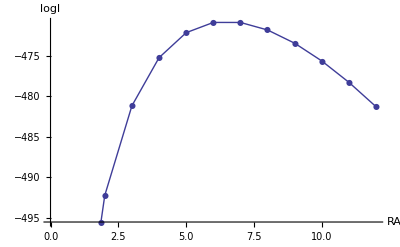

```mathematica
Clear[fun]
(*set pop ={omega_autosome,omega_sex} if both autosomes and sex chromosomes, pop={omega_autosome} if no sex chromsome, or pop={omega_sex} if no autosomes*)
magicSNPaa=Join[magicSNP[[{1}]],magicSNP[[2;;,Flatten[Position[magicSNP[[3]],_?(!MatchQ[#,"X"|"x"]&),{1},Heads->False]]]]];
fun[x_?NumericQ]:=Total[calOrigLogl[magicSNPaa,"indepModel",epsF,eps,{{0,0,0,x,0,x}}]];
ListPlot[Table[{x,fun[x]},{x,1,12,1}],Joined->True,PlotMarkers->{Automatic,8},AxesLabel->{"RA","logl"}]
```

```mathematica
FindMaximum[{fun[x],x>0},{x,Ra},StepMonitor:>PrintTemporary["x = ",x],MaxIterations->10,PrecisionGoal->3,AccuracyGoal->3];
Print["The estimated autosmal map expansion Ra = ",x/.%[[2]]]
```

The estimated autosmal map expansion Ra = 6.48457

## Estimate the sampling generation

List of mating schemes, where each scheme refer to the lines being sampled from a single generation.  In prior, the candicate generations in the schemelist is equally probable.

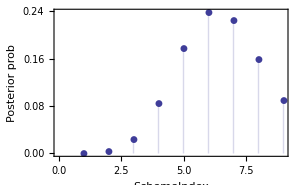
{SchemeIndex | PosteriorProb
6 | 0.23848
7 | 0.224992
5 | 0.177776
8 | 0.159077
9 | 0.0886901
4 | 0.0849102
3 | 0.0230531
2 | 0.00289732
1 | 0.000125107,-Graphics-}

```mathematica
schemelist=Table[Join[Table["Pairing",{2}],Table["Sibling",{i}]],{i,5,13}];
(*assuming all the sampled lines are from the same generation*)
issamegeneration =True; 
res=calOrigGeneration[magicSNP,model,epsF,eps,schemelist,issamegeneration];
{res//TableForm,ListPlot[res[[2;;]],ImageSize->300,PlotMarkers->Automatic,Filling->Axis,Frame->{{True,False},{True,False}},FrameLabel->{"SchemeIndex","Posterior prob"}]}
```

The estimated popScheme is given as follow; the maximum a posteriori estimation is very likely different from the true F11, for the small example data.

```mathematica
res[[2,1]]
schemelist[[%]]
Print["The estimated generation is F",Length[%]]
```

6

{Pairing,Pairing,Sibling,Sibling,Sibling,Sibling,Sibling,Sibling,Sibling,Sibling,Sibling,Sibling}

The estimated generation is F12

## Refereces

Zheng, C., Boer, M. P., and Eeuwijk, F. A. 2015. Reconstruction of genome ancestry blocks in multiparental populations. Submitted.

Zheng, C. 2015. Modeling X-linked ancestral origins in multiparental populations. G3: Genes | Genomes | Genetics. Early online.

Zheng, C., Boer, M. P., and Eeuwijk, F. A. 2014. A general modeling framework for genome ancestral origins in multi-parental populations. Genetics. 198: 87-101.